```mathematica
c=2;
Ln=4;
```

Probability l<c

```mathematica
P1[l_,p_]:=p^l*(1-p)
```

Probability c<=l<L

```mathematica
P2[l_,p_]:=p^l*(1-p)/2
```

Probability l=L

```mathematica
P3[L_,p_]:=p^L/2
```

```mathematica
T1=Evaluate@Table[P1[l,1/(1+2)],{l,0,c-1}]
```

{2/3,2/9}

```mathematica
T2=Evaluate@Table[P2[l,1/(1+2)],{l,c,Ln-1}]
```

{1/27,1/81}

```mathematica
T3=Evaluate@Table[P2[l,1/(1+2)],{l,c,Ln-1}]
```

{1/27,1/81}

```mathematica
T4=Flatten[{T1,T2,T3,P3[Ln,1/(1+2)],P3[Ln,1/(1+2)]}]
```

{2/3,2/9,1/27,1/81,1/27,1/81,1/162,1/162}

```mathematica
Total[T4]
```

1

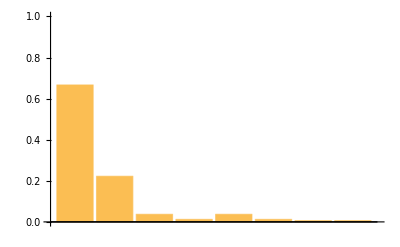

```mathematica
BarChart[T4,PlotRange->{0,1}]
```

```mathematica
c=2;
Ln=4;
```

Probability l<c

```mathematica
P1[l_,p_]:=p^l*(1-p)
```

Probability c<=l<L

```mathematica
P2[l_,p_]:=p^l*(1-p)/2
```

Probability l=L

```mathematica
P3[L_,p_]:=p^L/2
```

```mathematica
T1=Evaluate@Table[P1[l,1/(1+0.5)],{l,0,c-1}]
```

{0.333333,0.222222}

```mathematica
T2=Evaluate@Table[P2[l,1/(1+0.5)],{l,c,Ln-1}]
```

{0.0740741,0.0493827}

```mathematica
T3=Evaluate@Table[P2[l,1/(1+0.5)],{l,c,Ln-1}]
```

{0.0740741,0.0493827}

```mathematica
T4=Flatten[{T1,T2,T3,P3[Ln,1/(1+0.5)],P3[Ln,1/(1+0.5)]}]
```

{0.333333,0.222222,0.0740741,0.0493827,0.0740741,0.0493827,0.0987654,0.0987654}

```mathematica
Total[T4]
```

1.

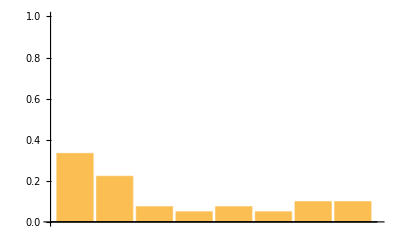

```mathematica
BarChart[T4,PlotRange->{0,1}]
```

```mathematica
c=2;
Ln=4;
```

Probability l<c

```mathematica
P1[l_,p_]:=p^l*(1-p)
```

Probability c<=l<L

```mathematica
P2[l_,p_]:=p^l*(1-p)/2
```

Probability l=L

```mathematica
P3[L_,p_]:=p^L/2
```

```mathematica
T1=Evaluate@Table[P1[l,1/(1+0.05)],{l,0,c-1}]
```

{0.047619,0.0453515}

```mathematica
T2=Evaluate@Table[P2[l,1/(1+0.05)],{l,c,Ln-1}]
```

{0.0215959,0.0205676}

```mathematica
T3=Evaluate@Table[P2[l,1/(1+0.05)],{l,c,Ln-1}]
```

{0.0215959,0.0205676}

```mathematica
T4=Flatten[{T1,T2,T3,P3[Ln,1/(1+0.05)],P3[Ln,1/(1+0.05)]}]
```

{0.047619,0.0453515,0.0215959,0.0205676,0.0215959,0.0205676,0.411351,0.411351}

```mathematica
Total[T4]
```

1.

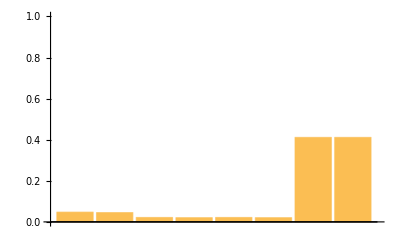

```mathematica
BarChart[T4,PlotRange->{0,1}]
```